```mathematica
ListaC={{0,4},
{1,5},
{2,1},
{3,4},
{4,3},
{5,5},
{6,1},
{7,2},
{8,4},
{9,1},
{10,1},
{11,3},
{12,4},
{13,5},
{14,3},
{15,5},
{16,8},
{17,4},
{18,12},
{19,13},
{20,13},
{21,21},
{22,16},
{23,20},
{24,26},
{25,27},
{26,20},
{27,32},
{28,22},
{29,35},
{30,47},
{31,38},
{32,54},
{33,56},
{34,59},
{35,59},
{36,67},
{37,88},
{38,73},
{39,108},
{40,116},
{41,132},
{42,155},
{43,160},
{44,158},
{45,164},
{46,186},
{47,215},
{48,250},
{49,307},
{50,284},
{51,340},
{52,381},
{53,441},
{54,456},
{55,496},
{56,536},
{57,551},
{58,576},
{59,655},
{60,701},
{61,802},
{62,803},
{63,852},
{64,849},
{65,870},
{66,909},
{67, 984},
{68,977},
{69,1002},
{70,1063},
{71,1083},
{72,1082},
{73,1083},
{74,1108},
{75,1078},
{76,1088},
{77,1047},
{78,1028},
{79,967},
{80,900},
{81,868},
{82,781},
{83,780},
{84,694},
{85,557},
{86,496},
{87,403},
{88,391},
{89,268},
{90,226},
{91,191},
{92,154},
{93,112},
{94,85},
{95,37},
{96,39},
{97,26},
{98,19},
{99,8},
{100,9},
{101,8},
{102,2},
{103,2},
{104,2}}
```

{{0,4},{1,5},{2,1},{3,4},{4,3},{5,5},{6,1},{7,2},{8,4},{9,1},{10,1},{11,3},{12,4},{13,5},{14,3},{15,5},{16,8},{17,4},{18,12},{19,13},{20,13},{21,21},{22,16},{23,20},{24,26},{25,27},{26,20},{27,32},{28,22},{29,35},{30,47},{31,38},{32,54},{33,56},{34,59},{35,59},{36,67},{37,88},{38,73},{39,108},{40,116},{41,132},{42,155},{43,160},{44,158},{45,164},{46,186},{47,215},{48,250},{49,307},{50,284},{51,340},{52,381},{53,441},{54,456},{55,496},{56,536},{57,551},{58,576},{59,655},{60,701},{61,802},{62,803},{63,852},{64,849},{65,870},{66,909},{67,984},{68,977},{69,1002},{70,1063},{71,1083},{72,1082},{73,1083},{74,1108},{75,1078},{76,1088},{77,1047},{78,1028},{79,967},{80,900},{81,868},{82,781},{83,780},{84,694},{85,557},{86,496},{87,403},{88,391},{89,268},{90,226},{91,191},{92,154},{93,112},{94,85},{95,37},{96,39},{97,26},{98,19},{99,8},{100,9},{101,8},{102,2},{103,2},{104,2}}

```mathematica
L=Length[ListaC]
```

105

```mathematica
∑_(j=1)^L ListaC[[j]][[2]]
```

33962

```mathematica
μ=N[∑_(j=1)^L ((ListaC[[j]][[1]]*ListaC[[j]][[2]])/33962)]
```

68.5746

```mathematica
σ=N[√(∑_(j=1)^L (((ListaC[[j]][[1]]-μ)^2*ListaC[[j]][[2]])/33962))]
```

13.2311

```mathematica
Length[ListaC]
```

105

```mathematica
Lista2=Table[{ListaC[[j]][[1]],(ListaC[[j]][[2]])/33962},{j,1,Length[ListaC]}];
```

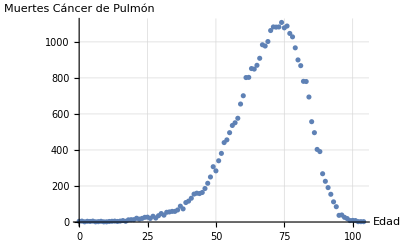

```mathematica
g1=ListPlot[ListaC ,GridLines->Automatic,AxesLabel->{"Edad","Muertes Cáncer de Pulmón"}]
```

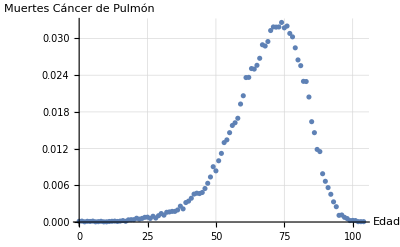

```mathematica
g3=ListPlot[Lista2 ,GridLines->Automatic,AxesLabel->{"Edad","Muertes Cáncer de Pulmón"}]
```

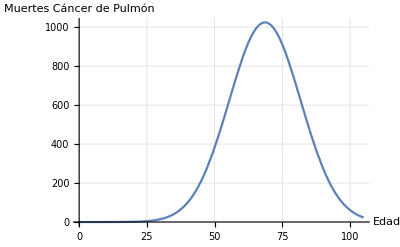

```mathematica
g2=Plot[33962*1/(√(2π)σ) ⅇ^(-(x-μ)^2/(2 σ^2)),{x,0,105},GridLines->Automatic,AxesLabel->{"Edad","Muertes Cáncer de Pulmón"}]
```

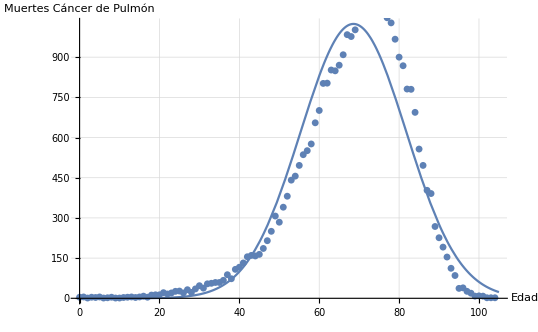

```mathematica
Show[g2,g1]
```